```mathematica
l0:={{1},{0}}
l1:={{0},{1}}
```

```mathematica
k0000:=KroneckerProduct[KroneckerProduct[KroneckerProduct[l0,l0],l0],l0]
k1001:=KroneckerProduct[KroneckerProduct[KroneckerProduct[l1,l0],l0],l1]
k0100:=KroneckerProduct[KroneckerProduct[KroneckerProduct[l0,l1],l0],l0]
k1111:=KroneckerProduct[KroneckerProduct[KroneckerProduct[l1,l1],l1],l1]
b0000:=Transpose[k0000]
b1001:=Transpose[k1001]
b0100:=Transpose[k0100]
b1111:=Transpose[k1111]
```

```mathematica
H[g_]:=1/(2g^2){{0,0,0,0,0,0,0,-2,0,0,0,0,0,-2,0,0},{0,3g^4/4,0,0,0,0,-2,0,0,0,0,0,-2,0,0,0},{0,0,3g^4/2,0,0,-2,0,0,0,0,0,0,0,0,0,-1/2},{0,0,0,9g^4/4,-2,0,0,0,0,0,0,0,0,0,-1/2,0},{0,0,0,-2,3g^4/4,0,0,0,0,-2,0,0,0,0,0,0},{0,0,-2,0,0,3g^4/2,0,0,-2,0,0,0,0,0,0,0},{0,-2,0,0,0,0,9g^4/4,0,0,0,0,-1/2,0,0,0,0},{-2,0,0,0,0,0,0,3g^4,0,0,-1/2,0,0,0,0,0},{0,0,0,0,0,-2,0,0,3g^4/2,0,0,0,0,0,0,-1/2},{0,0,0,0,-2,0,0,0,0,9g^4/4,0,0,0,0,-1/2,0},{0,0,0,0,0,0,0,-1/2,0,0,3g^4,0,0,-1/2,0,0},{0,0,0,0,0,0,-1/2,0,0,0,0,15g^4/4,-1/2,0,0,0},{0,-2,0,0,0,0,0,0,0,0,0,-1/2,9g^4/4,0,0,0},{-2,0,0,0,0,0,0,0,0,0,-1/2,0,0,3g^4,0,0},{0,0,0,-1/2,0,0,0,0,0,-1/2,0,0,0,0,15g^4/4,0},{0,0,-1/2,0,0,0,0,0,-1/2,0,0,0,0,0,0,9g^4/2}}+500IdentityMatrix[16]
```

```mathematica
GS[g_]:=Part[Eigenvectors[H[g]],16]
```

```mathematica
RDM[g_]:=Part[GS[g],1]^2k0000.b0000+Part[GS[g],8]^2k1001.b1001+Part[GS[g],11]^2k0100.b0100+Part[GS[g],14]^2k1111.b1111+Part[GS[g],1]Part[GS[g],14]k0000.b1111+Part[GS[g],14]Part[GS[g],1]k1111.b0000
```

```mathematica
S[g_]:=-Part[Eigenvalues[RDM[g]],1]Log[2,Part[Eigenvalues[RDM[g]],1]]-Part[Eigenvalues[RDM[g]],2]Log[2,Part[Eigenvalues[RDM[g]],2]]-Part[Eigenvalues[RDM[g]],3]Log[2,Part[Eigenvalues[RDM[g]],3]]
```

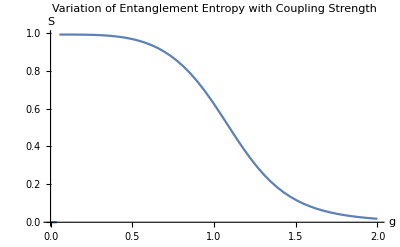

```mathematica
Plot[S[g],{g,0,2},AxesLabel->{"g","S"},PlotLabel->"Variation of Entanglement Entropy with Coupling Strength"]
```

```mathematica
Manipulate[S[g],{g,0.054,2}]
```

```mathematica
Udiag:={{0,1},{1,0}}
Uoff:={{0,1},{-1,0}}
```

```mathematica
Plaq1:=KroneckerProduct[KroneckerProduct[KroneckerProduct[Udiag,Udiag],Udiag],Udiag]
Plaq2:=KroneckerProduct[KroneckerProduct[KroneckerProduct[Udiag,Udiag],Uoff],Uoff]
Plaq3:=KroneckerProduct[KroneckerProduct[KroneckerProduct[Udiag,Uoff],Uoff],Udiag]
Plaq4:=KroneckerProduct[KroneckerProduct[KroneckerProduct[Udiag,Uoff],Udiag],Uoff]
Plaq5:=KroneckerProduct[KroneckerProduct[KroneckerProduct[Uoff,Uoff],Udiag],Udiag]
Plaq6:=KroneckerProduct[KroneckerProduct[KroneckerProduct[Uoff,Uoff],Uoff],Uoff]
Plaq7:=KroneckerProduct[KroneckerProduct[KroneckerProduct[Uoff,Udiag],Uoff],Udiag]
Plaq8:=KroneckerProduct[KroneckerProduct[KroneckerProduct[Uoff,Udiag],Udiag],Uoff]
```

```mathematica
B:=Plaq1+Plaq2+Plaq3+Plaq4+Plaq5+Plaq6+Plaq7+Plaq8
```

```mathematica
KroneckerProduct[Udiag,Udiag]//MatrixForm
```

(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)

```mathematica
KroneckerProduct[KroneckerProduct[Udiag,Udiag],Udiag]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Plaq1//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)